# Linear Regression Model Initialization

## Defining a Function to create Linear Regression Neural Network

#### Explanation

When we create a neural network with each layer having a fully linear activation function (LinearLayer), each layer simply outputs a linear combination of the outputs of the previous layer. Mathematically, this shows itself as 

Layer Output 

where  is a matrix of weights and  is the value of the bias. It’s important to note that you could apply this operation infinite times and the output would still be a linear combination of the original weights and biases. This portion of the project will examine how changes in the distributions of weights and biases affect the outputs of a linear regression neural network and how the behavior changes with varying depths.

```mathematica
LinearRegressionNetworkPlot[depths_,distributionType_,params_]:=Module[{netInit,f,plots,depth,distribution,title},distribution=Switch[distributionType,"Normal",NormalDistribution[params[[1]],params[[2]]],"Uniform",UniformDistribution[{-params[[1]],params[[1]]}],"Gamma",GammaDistribution[params[[1]],params[[2]]],_,NormalDistribution[0,1]];
SeedRandom[1234];
title="Outputs of Linear Regression Network with Weights initialized from a "<>distributionType <> " distribution.";
plots=Table[With[{netInit=NetChain[Append[Catenate@Table[{3,LinearLayer[3]},depth],LinearLayer[1]],"Input"->{3}]},Column[{Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->distribution,"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[{x,x,x}];
SetAttributes[f,Listable];
f[x]],15],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None],Style["depth = "<>ToString[depth],Italic,12,Gray]}]],{depth,depths}];
Column[{Style[title,Bold,14],Row[Riffle[plots,Spacer[20]]]}]]
```

#### Explanation

This function generates plots of outputs for 15 runs of neural networks with inputted depth that have weights generated from an inputted distribution (either Normal, Gamma, or Uniform), and based on the distribution type, takes either one or two parameters for generating the distribution. It then plots the outputs of each run of the neural network for each of the inputted depths, showing a clear progression of the complexity of outputs as depth increases.

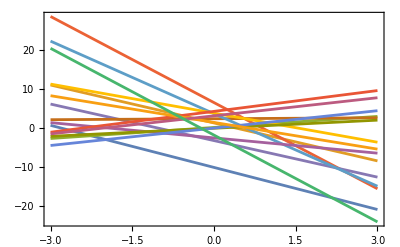
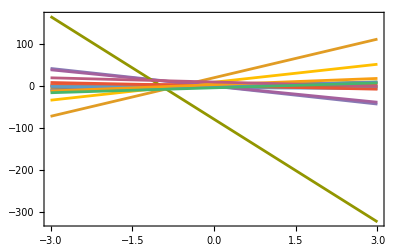
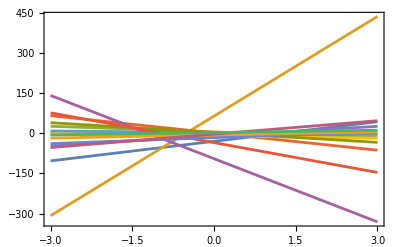
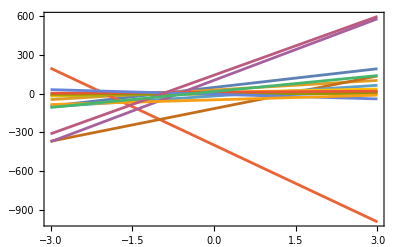
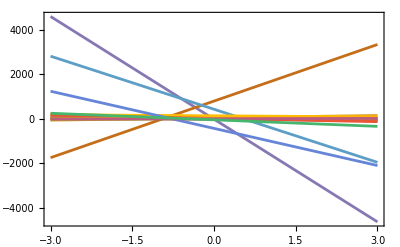
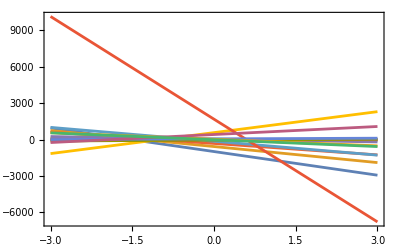
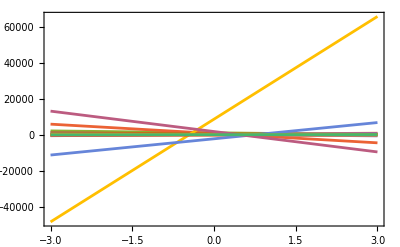
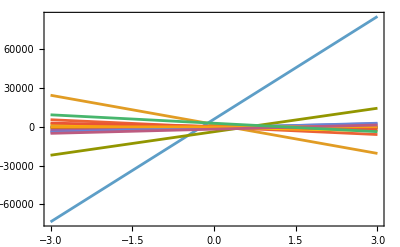
Outputs of Linear Regression Network with Weights initialized from a Normaldistribution.
-Graphics-
depth = 1-Graphics-
depth = 2-Graphics-
depth = 3-Graphics-
depth = 4-Graphics-
depth = 5-Graphics-
depth = 6-Graphics-
depth = 7-Graphics-
depth = 8

```mathematica
LinearRegressionNetworkPlot[Range[10],"Normal",{0,1}]
```

#### Explanation

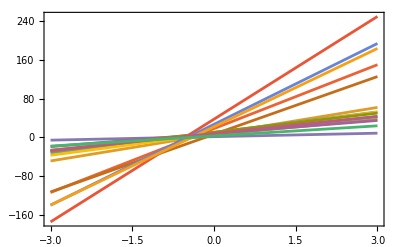
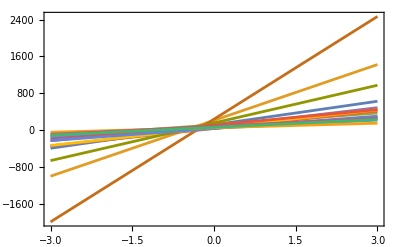
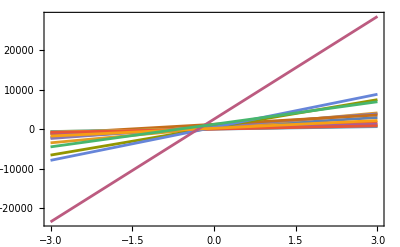
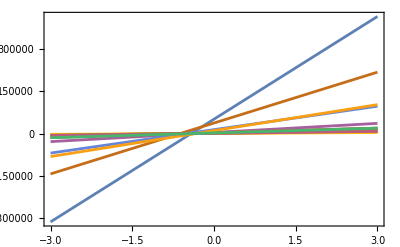
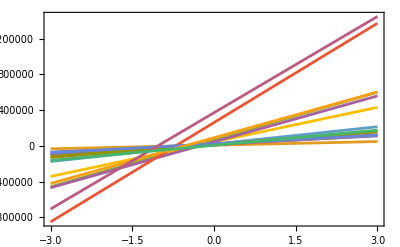
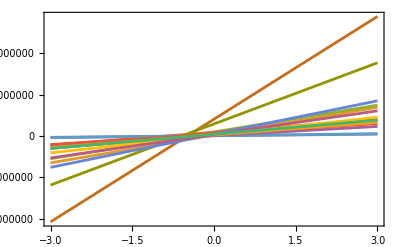
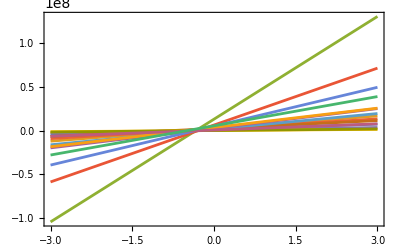
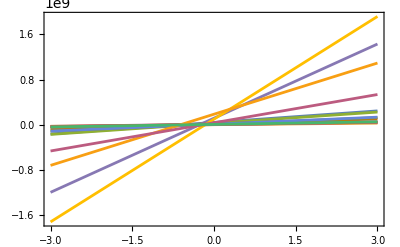
Outputs of Linear Regression Network with Weights initialized from a Gamma distribution.
-Graphics-
depth = 1-Graphics-
depth = 2-Graphics-
depth = 3-Graphics-
depth = 4-Graphics-
depth = 5-Graphics-
depth = 6-Graphics-
depth = 7-Graphics-
depth = 8

```mathematica
LinearRegressionNetworkPlot[Range[8],"Gamma",{1,1}]
```

#### Explanation

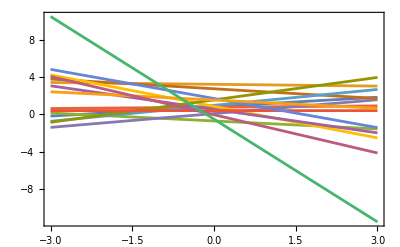
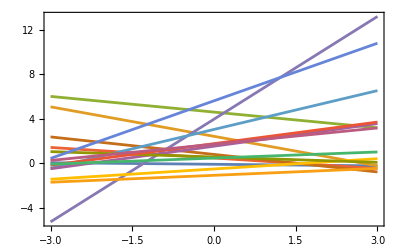
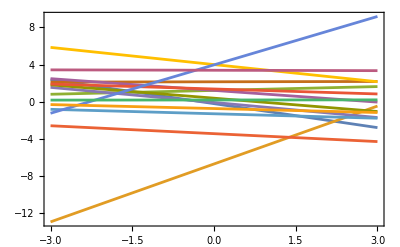
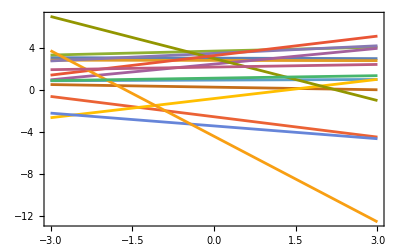
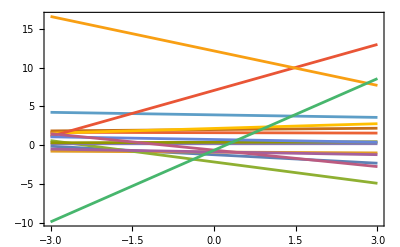
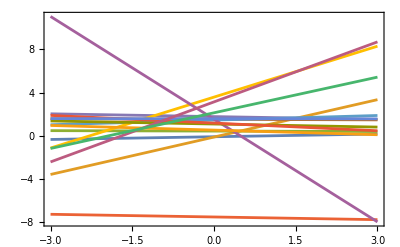
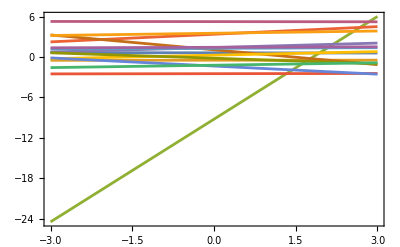
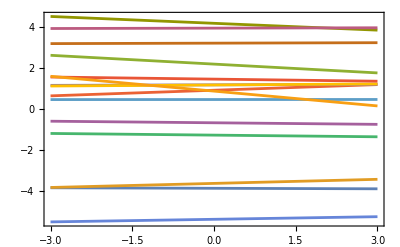
Outputs of Linear Regression Network with Weights initialized from a Uniform distribution.
-Graphics-
depth = 1-Graphics-
depth = 2-Graphics-
depth = 3-Graphics-
depth = 4-Graphics-
depth = 5-Graphics-
depth = 6-Graphics-
depth = 7-Graphics-
depth = 8

```mathematica
LinearRegressionNetworkPlot[Range[8],"Uniform",{1}]
```

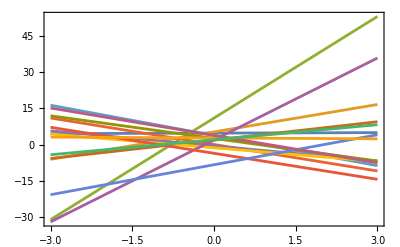
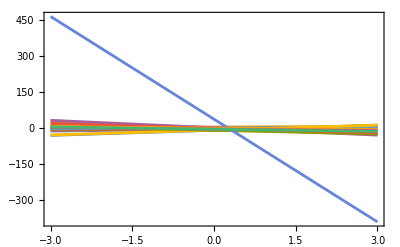
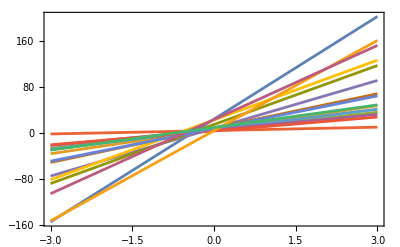
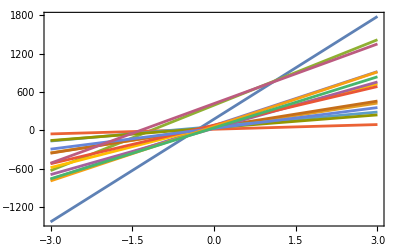
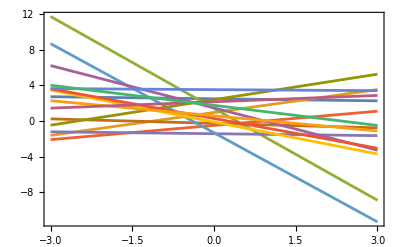
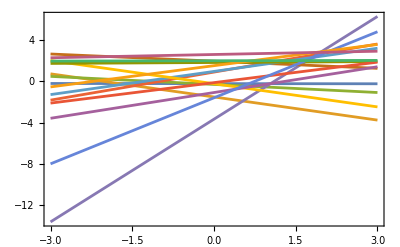
Outputs of Linear Regression Network with Weights initialized from a Normal distribution
-Graphics-
depth = 1-Graphics-
depth = 2
Outputs of Linear Regression Network with Weights initialized from a Gamma distribution
-Graphics-
depth = 1-Graphics-
depth = 2
Outputs of Linear Regression Network with Weights initialized from a Uniform distribution
-Graphics-
depth = 1-Graphics-
depth = 2

```mathematica
Column[{LinearRegressionNetworkPlot[Range[2],"Normal",{0,1}], LinearRegressionNetworkPlot[Range[2],"Gamma",{1,1}],LinearRegressionNetworkPlot[Range[2],"Uniform",{1}]}]
```

#### Explanation

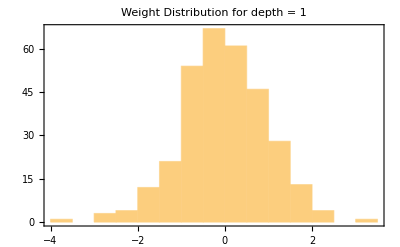
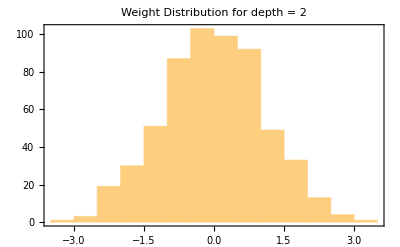
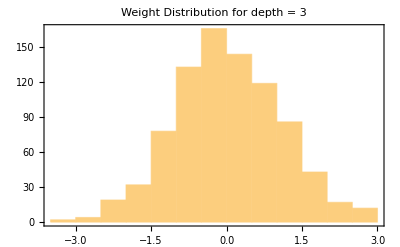
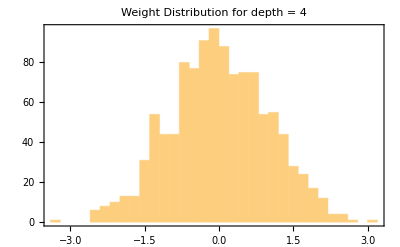
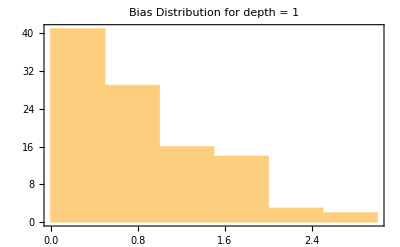
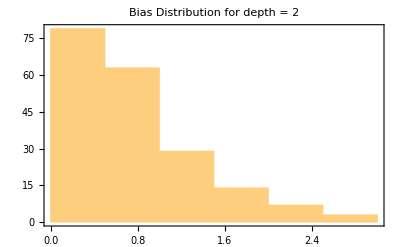
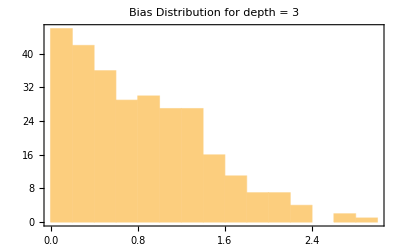
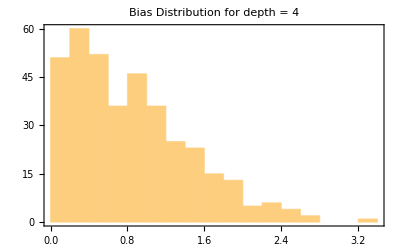
Weight and Bias Distributions
-Graphics-


-Graphics-


-Graphics-


-Graphics-

-Graphics-


-Graphics-


-Graphics-


-Graphics-

```mathematica
WeightBiasDistributionHistograms[depths_,distributionType_,params_]:=Module[{netInit,distribution,weightPlots,biasPlots,weights,biases},distribution=Switch[distributionType,"Normal",NormalDistribution[params[[1]],params[[2]]],"Uniform",UniformDistribution[{-params[[1]],params[[1]]}],"Gamma",GammaDistribution[params[[1]],params[[2]]],_,NormalDistribution[0,1]];
SeedRandom[1234];
weights=Table[Flatten[Table[Module[{net=NetInitialize[NetChain[Append[Catenate@Table[{3,LinearLayer[3]},depth],LinearLayer[1]],"Input"->{3}],Method->{"Random","Weights"->distribution,"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic]},Normal[NetExtract[net,{All,"Weights"}]]],15]],{depth,depths}];
biases=Table[Flatten[Table[Module[{net=NetInitialize[NetChain[Append[Catenate@Table[{3,LinearLayer[3]},depth],LinearLayer[1]],"Input"->{3}],Method->{"Random","Weights"->distribution,"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic]},Normal[NetExtract[net,{All,"Biases"}]]],15]],{depth,depths}];
weightPlots=Table[Column[{Histogram[weights[[i]],PlotLabel->"Weight Distribution for depth = "<>ToString[depths[[i]]],Frame->True],Spacer[20]}],{i,Length[depths]}];
biasPlots=Table[Column[{Histogram[biases[[i]],PlotLabel->"Bias Distribution for depth = "<>ToString[depths[[i]]],Frame->True],Spacer[20]}],{i,Length[depths]}];
Column[{Style["Weight and Bias Distributions",Bold,14],Column[Riffle[weightPlots,Spacer[30]]],Column[Riffle[biasPlots,Spacer[30]]]}]]

WeightBiasDistributionHistograms[{1,2,3,4},"Normal",{0,1}]
```

```mathematica
WeightOutputDistributionHistograms[depths_,distributionType_,params_]:=Module[{netInit,distribution,weightPlots,outputPlots,weights,outputs,testInput},distribution=Switch[distributionType,"Normal",NormalDistribution[params[[1]],params[[2]]],"Uniform",UniformDistribution[{-params[[1]],params[[1]]}],"Gamma",GammaDistribution[params[[1]],params[[2]]],_,NormalDistribution[0,1]];
SeedRandom[1234];
testInput=ConstantArray[0,{100,3}];(*Generating 100 input vectors of zeros with 3 features each*)weights=Table[Flatten[Table[Module[{net=NetInitialize[NetChain[Append[Catenate@Table[{3,LinearLayer[3]},depth],LinearLayer[1]],"Input"->{3}],Method->{"Random","Weights"->distribution,"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic]},Normal[NetExtract[net,{All,"Weights"}]]],15]],{depth,depths}];
outputs=Table[Flatten[Table[Module[{net=NetInitialize[NetChain[Append[Catenate@Table[{3,LinearLayer[3]},depth],LinearLayer[1]],"Input"->{3}],Method->{"Random","Weights"->distribution,"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic]},Normal[net[testInput]]],15]],{depth,depths}];
weightPlots=Table[Column[{Histogram[weights[[i]],PlotLabel->"Weight Distribution for depth = "<>ToString[depths[[i]]],Frame->True],Spacer[20]}],{i,Length[depths]}];
outputPlots=Table[Column[{Histogram[outputs[[i]],PlotLabel->"Output Distribution for depth = "<>ToString[depths[[i]]],Frame->True],Spacer[20]}],{i,Length[depths]}];
Column[{Style["Weight and Output Distributions",Bold,14],Column[Riffle[weightPlots,Spacer[30]]],Column[Riffle[outputPlots,Spacer[30]]]}]]
```

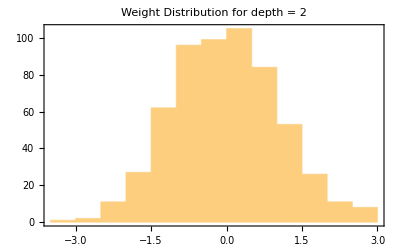
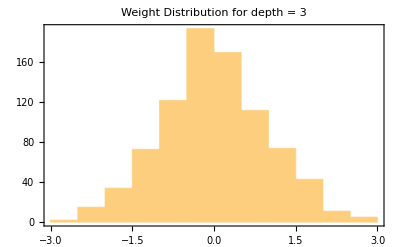
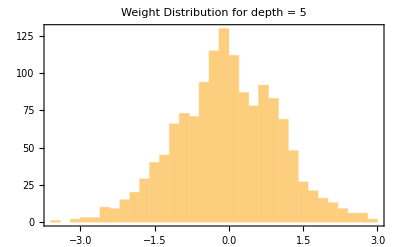
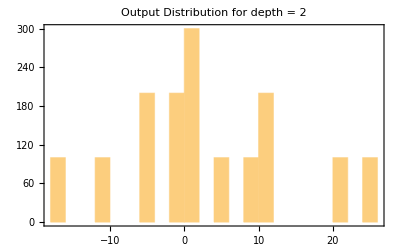
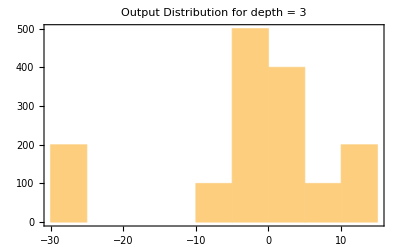
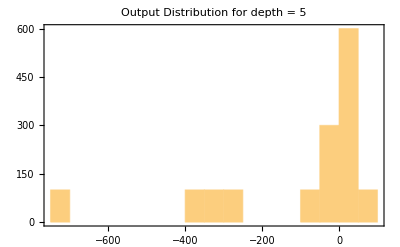
Weight and Output Distributions
-Graphics-


-Graphics-


-Graphics-

-Graphics-


-Graphics-


-Graphics-

```mathematica
WeightOutputDistributionHistograms[{2,3,5},"Normal",{0,1}]
```

```mathematica
WeightOutputDistributionHistograms[depths_,distributionType_,params_]:=Module[{netInit,distribution,weightPlots,outputPlots,weights,outputs,testInput,title},distribution=Switch[distributionType,"Normal",NormalDistribution[params[[1]],params[[2]]],"Uniform",UniformDistribution[{-params[[1]],params[[1]]}],"Gamma",GammaDistribution[params[[1]],params[[2]]],_,NormalDistribution[0,1]];
SeedRandom[1234];
testInput=Table[{x,x,x},{x,-3,3,0.1}];title="Outputs of Neural Network with Weights initialized from a "<>distributionType<>" distribution.";
weights=Table[Flatten[Module[{net=NetInitialize[NetChain[Append[Catenate@Table[{3,LinearLayer[3]},depth],LinearLayer[1]],"Input"->{3}],Method->{"Random","Weights"->distribution,"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic]},Normal[NetExtract[net,{All,"Weights"}]]]],{depth,depths}];
outputs=Table[Module[{net=NetInitialize[NetChain[Append[Catenate@Table[{3,LinearLayer[3]},depth],LinearLayer[1]],"Input"->{3}],Method->{"Random","Weights"->distribution,"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[{x,x,x}];
SetAttributes[f,Listable];
Plot[f[testInput],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None,PlotLabel->"Output for depth = "<>ToString[depth]]],{depth,depths}];
weightPlots=Table[Histogram[weights[[i]],PlotLabel->"Weight Distribution for depth = "<>ToString[depths[[i]]],Frame->True],{i,Length[depths]}];
Column[{Style["Weight and Output Distributions",Bold,14],Column[Riffle[weightPlots,Spacer[30]]],Column[Riffle[outputs,Spacer[30]]]}]]
```

```mathematica
WeightOutputDistributionHistograms[{2},"Normal",{0,1}]
```

```mathematica
Manipulate[Module[{netInit,f,plots,title,net,distribution},title="Outputs of Linear Regression Network with Weights initialized from "<>distributionType<>" Distribution";
distribution=Which[distributionType=="Normal",NormalDistribution[0,stdDev],distributionType=="Gamma",GammaDistribution[alpha,beta],distributionType=="Uniform",UniformDistribution[{-range,range}]];
netInit=NetChain[Append[Catenate@Table[{3,LinearLayer[3]},depth],LinearLayer[1]],"Input"->{3}];
plots=Table[net=NetInitialize[netInit,Method->{"Random","Weights"->distribution},RandomSeeding->seed];
f[x_?NumericQ]:=net[{x,x,x}];
SetAttributes[f,Listable];
Plot[f[x],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None,PlotStyle->ColorData[1][seed]],{seed,1,15}];
Column[{Style[title,Bold,14],Show[plots,PlotLegends->"Expressions"],Style["depth = "<>ToString[depth],Italic,12,Gray]}]],{{distributionType,"Normal","Distribution Type"},{"Normal","Gamma","Uniform"}},{{depth,1,"Depth"},1,10,1},{{stdDev,1,"Standard Deviation"},0.5,5,0.5,Appearance->If[distributionType=="Normal","Open","None"]},{{alpha,1,"Alpha (Gamma)"},0.5,5,0.5,Appearance->If[distributionType=="Gamma","Open","None"]},{{beta,1,"Beta (Gamma)"},0.5,5,0.5,Appearance->If[distributionType=="Gamma","Open","None"]},{{range,1,"Range (Uniform)"},0.5,5,0.5,Appearance->If[distributionType=="Uniform","Open","None"]}]
```

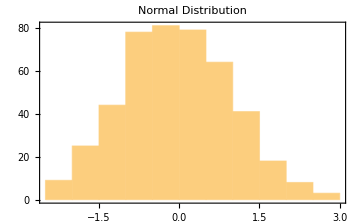
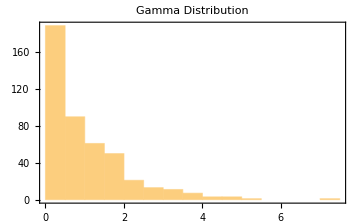
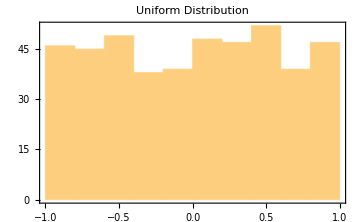

```mathematica
WeightDistributionHistogram[distributionTypes_,params_]:=Module[{distribution,weightPlots,weights,distributions},distributions=MapThread[Switch[#1,"Normal",NormalDistribution[#2[[1]],#2[[2]]],"Uniform",UniformDistribution[{-#2[[1]],#2[[1]]}],"Gamma",GammaDistribution[#2[[1]],#2[[2]]],_,NormalDistribution[0,1]]&,{distributionTypes,params}];
SeedRandom[1234];
weights=Table[Flatten[Table[Module[{net=NetInitialize[NetChain[{3,LinearLayer[3],LinearLayer[3],LinearLayer[1]},"Input"->{3}],Method->{"Random","Weights"->distribution},RandomSeeding->Automatic]},Normal[NetExtract[net,{All,"Weights"}]]],15]],{distribution,distributions}];
weightPlots=Table[Column[{Histogram[weights[[i]],PlotLabel->distributionTypes[[i]]<>" Distribution",Frame->True,ImageSize->Medium]}],{i,Length[distributionTypes]}];
Row[weightPlots,Spacer[10]]]

WeightDistributionHistogram[{"Normal","Gamma","Uniform"},{{0,1},{1,1},{1}}]
```

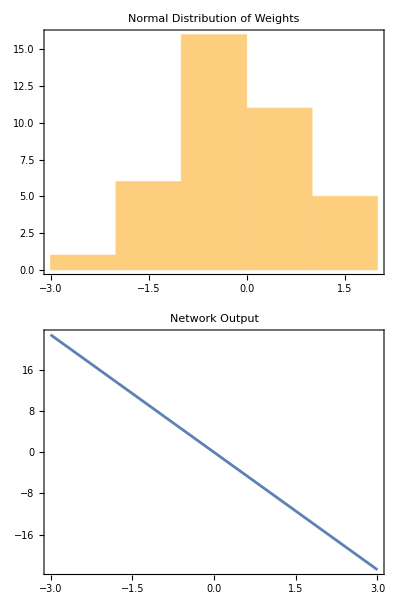

```mathematica
WeightDistributionAndOutputPlot[depth_,distributionType_,params_]:=Module[{distribution,weights,net,inputData,outputData},distribution=Switch[distributionType,"Normal",NormalDistribution[params[[1]],params[[2]]],"Uniform",UniformDistribution[{-params[[1]],params[[1]]}],"Gamma",GammaDistribution[params[[1]],params[[2]]],_,NormalDistribution[0,1]];
SeedRandom[1234];
net=NetInitialize[NetChain[Append[Catenate@Table[{3,LinearLayer[3]},depth],LinearLayer[1]],"Input"->{3}],Method->{"Random","Weights"->distribution},RandomSeeding->Automatic];
weights=Flatten[Normal[NetExtract[net,{All,"Weights"}]]];
inputData=Table[{x,0,0},{x,-3,3,0.1}];
outputData=net[inputData];
Column[{Histogram[weights,PlotLabel->distributionType<>" Distribution of Weights",Frame->True,ImageSize->Small],ListPlot[Transpose[{Range[-3,3,0.1],Flatten[outputData]}],PlotLabel->"Network Output",Frame->True,ImageSize->Small,Joined->True]}]]

WeightDistributionAndOutputPlot[2,"Normal",{0,1}]
```

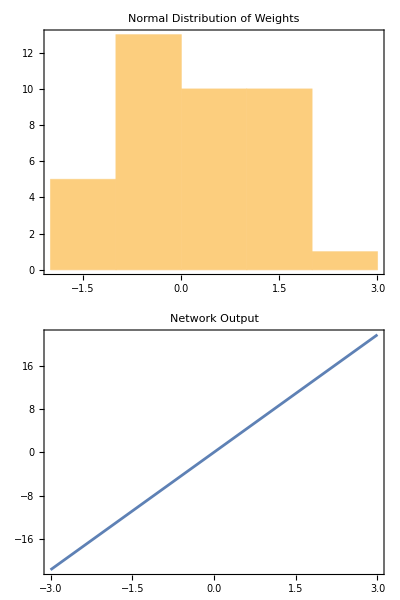
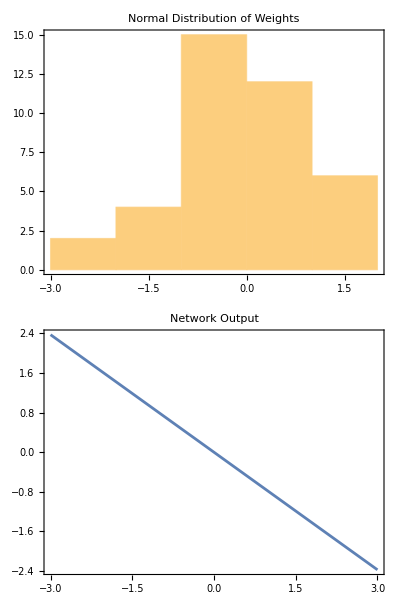
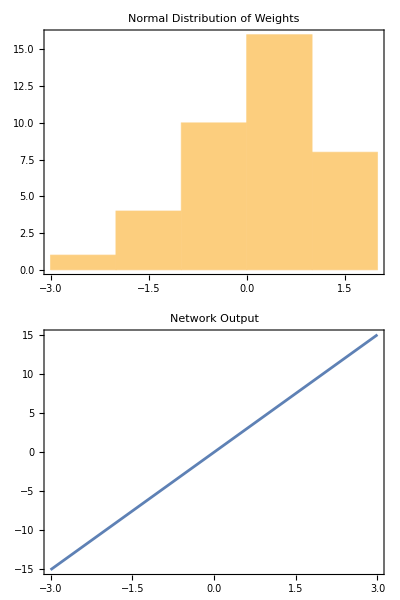
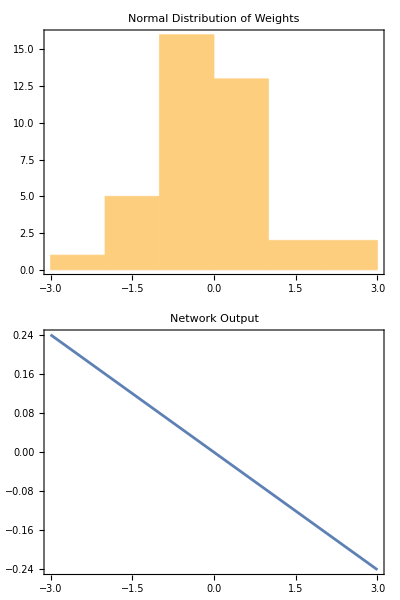
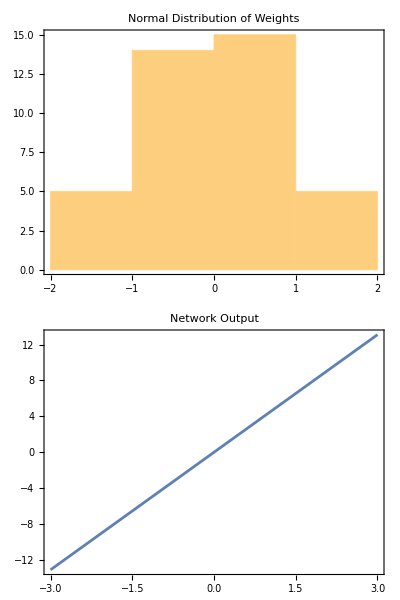

```mathematica
Column[Table[WeightDistributionAndOutputPlot[2,"Normal",{0,1}],5]]
```

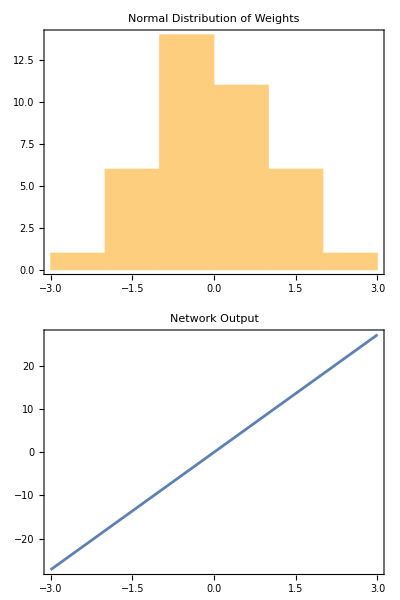
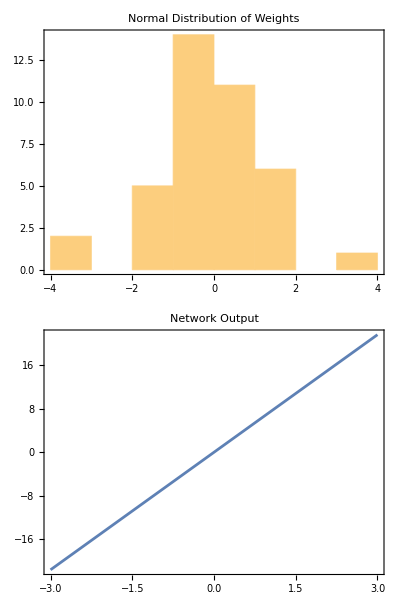
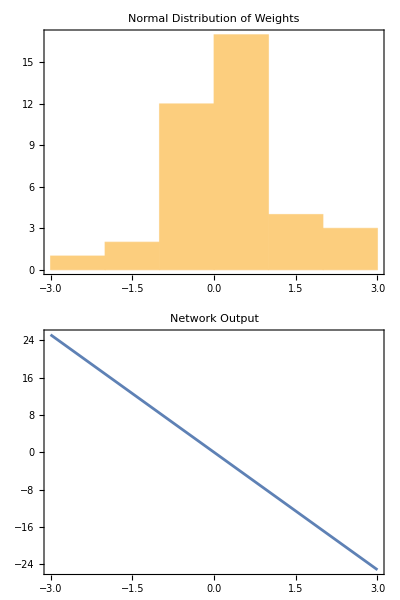
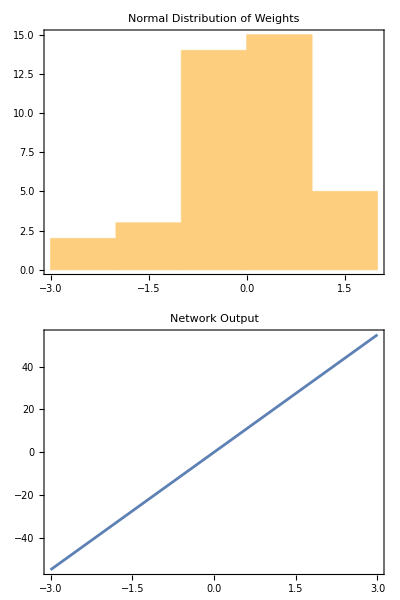
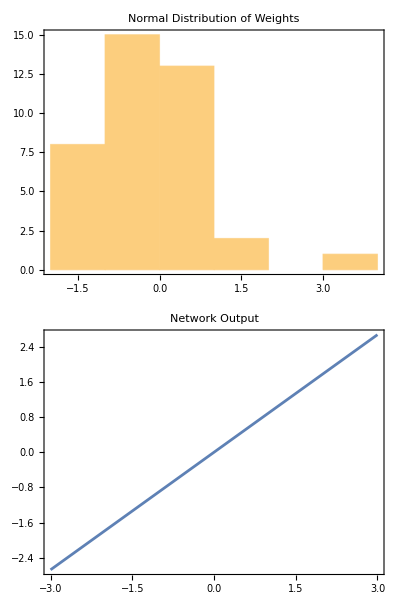

```mathematica
WeightDistributionAndOutputPlot[depth_,distributionType_,params_]:=Module[{distribution,weights,net,inputData,outputData},distribution=Switch[distributionType,"Normal",NormalDistribution[params[[1]],params[[2]]],"Uniform",UniformDistribution[{-params[[1]],params[[1]]}],"Gamma",GammaDistribution[params[[1]],params[[2]]],_,NormalDistribution[0,1]];
SeedRandom[1234];
net=NetInitialize[NetChain[Append[Catenate@Table[{3,LinearLayer[3]},depth],LinearLayer[1]],"Input"->{3}],Method->{"Random","Weights"->distribution},RandomSeeding->Automatic];
weights=Flatten[Normal[NetExtract[net,{All,"Weights"}]]];
inputData=Table[{x,0,0},{x,-3,3,0.1}];
outputData=net[inputData];
Column[{Histogram[weights,PlotLabel->distributionType<>" Distribution of Weights",Frame->True,ImageSize->Small],ListPlot[Transpose[{Range[-3,3,0.1],Flatten[outputData]}],PlotLabel->"Network Output",Frame->True,ImageSize->Small,Joined->True]}]]

Row[Table[WeightDistributionAndOutputPlot[2,"Normal",{0,1}],5], Spacer[10]]
```

```mathematica
WeightDistributionAndOutputPlot[depth_,distributionType_,params_]:=Module[{distribution,weights,net,inputData,outputData},distribution=Switch[distributionType,"Normal",NormalDistribution[params[[1]],params[[2]]],"Uniform",UniformDistribution[{-params[[1]],params[[1]]}],"Gamma",GammaDistribution[params[[1]],params[[2]]],_,NormalDistribution[0,1]];
SeedRandom[1234];
net=NetInitialize[NetChain[Append[Catenate@Table[{3,LinearLayer[3]},depth],LinearLayer[1]],"Input"->{3}],Method->{"Random","Weights"->distribution},RandomSeeding->Automatic];
weights=Flatten[Normal[NetExtract[net,{All,"Weights"}]]];
inputData=Table[{x,0,0},{x,-3,3,0.1}];
outputData=net[inputData];
Column[{Histogram[weights,PlotLabel->distributionType<>" Distribution of Weights",Frame->True,ImageSize->{250, 150}],ListPlot[Transpose[{Range[-3,3,0.1],Flatten[outputData]}],PlotLabel->"Network Output",Frame->True,ImageSize->{250, 150},Joined->True]}]]

Rasterize[Row[Flatten[Table[Table[WeightDistributionAndOutputPlot[2,distribution,Switch[distribution,"Normal",{0,1},"Uniform",{1},"Gamma",{1,1}]],3],{distribution,{"Normal","Uniform","Gamma"}}]]]]
```

-Graphics-